1Intro to Med Chem

Robert R. Gotwals, Jr.

NCSSM Chemistry

NCSSM Online

## Section 1: Basic Concepts

Medicinal chemistry is the study of how drugs are discovered or designed, synthesized in the laboratory, and evaluated for their effectiveness to cure illnesses, reduce or relieve pain, or prevent some disease from happening in the first place.  Medicinal chemistry has connections with other disciplines, including pharmacology and the pharmaceutical sciences.  Medicinal chemistry is also an interdisciplinary science, in that it requires a background not only in chemistry, but also in mathematics (especially statistics), computing (especially computational chemistry and physical chemistry), and biology (especially biochemistry, protein biology and genetics/genomics).  In this course, all of these disciplines will be used.  Most of the time, the talented medicinal chemist needs to be able to use several of these together and at the correct time.  It's very much like having a toolbox with a hammer, saw, screwdriver, and some specialty tools.  You have to know what each tool does individually, and how to use some or all of the tools at the right time, depending on the job to be done.

here is a remark!

Perhaps we can begin our exploration of medicinal chemistry with an example.  Figure 1 shows a cartoon schematic of how a drug is designed to fit into a protein receptor site.  On the left, a protein enzyme known as purine nucleoside phosphorylase, or PNP, is shown binding to another protein, shown  in blue.  The PNP enzyme catalyzes, or changes, the behavior of the blue receptor protein.  This change, or activation, can lead to diseases such as an immune system deficiency.  We want to design a drug, shown in green on the right, that will block the PNP enzyme, resulting in the prevention of this immune system deficiency.  The designed drug needs to be the right shape, size, and chemical makeup to be more likely to fill the receptor space than the endogenous, or natural, PNP enzyme molecule.  Notice that, with the drug in place, there is nowhere for the PNP enzyme to fit in the receptor protein!

Figure 1.  Cartoon schematic of the drug design process.  In this graphic, we are trying to design a drug (shown in green on the right) that will "fit" into a protein (shown in blue).  The protein is known as a "receptor", and the drug is known as a "ligand".

The protein is an enzyme, meaning that it functions as a molecular machine, causing some process or reaction to happen in the body, usually in the cells.  Other proteins serve as building blocks for making tissues and other components of living organisms.  The PNP protein is shown below:  if you are reading this with Mathematica, then the protein is interactive, and you can rotate it.  The cartoon twists, arrows, and ribbons are describing the secondary structure of the protein. This protein structure was downloaded from the Protein Data Bank.  Protein structures from this database are all given a 4-character identification number, and are of the filetype ".pdb".  This structure is 1m73.pdb.  In the literature, you will frequently see the notation "[PDB:1m73]" used to indicate the identification number, or PDB number, of the protein structure.

```mathematica
Import["/Users/gotwals/Desktop/IntroMedChem/Chapter 1/1M73.pdb"]
```

-Graphics3D-

Drug compounds are almost always organic compounds, consisting of carbon and hydrogen atoms, and oftentimes with other atoms such as nitrogen, chlorine, sulfur, and phosphorus.  The organic compound labeled purine in Figure 1 is an organic compound that consists of two ring structures, one with six atoms and the other with five atoms.  Our drug prevents the purine, sugar group, and phosphate group from occupying the space.  We hope that that blocking action results in a cure for our patient!

So, you should understand that you will need some background in organic chemistry, and we will spend the first part of the course learning how to identify the building blocks of organic molecules (known as functional groups), and a little bit on how to name organic compounds.

Organic chemistry is not difficult, but there is a tremendous amount of jargon to be learned, and that requires time, patience, and hard work.  For example, in Figure 2, we have identified four different types of carbons -- primary, secondary, tertiary, and quaternary -- that will determine how this organic compound might interact with other molecules in the body.  Too many of one type of carbon, and the drug may cause side effects.  Too few, and it won't cure the patient.  Being able to identify carbon types will be important in your study of medicinal chemistry.

Figure 2:  Sample molecule showing four types of structural carbons

In organic chemistry, it is also important to know where and how the functional groups are attached.  Suppose we have four fictitious functional groups -- A, B, C, and D -- that are attached to a carbon in the middle.  The "wedges" -- the solid and dashed triangles -- show the three dimensional structure of this compound.  The solid wedges are coming out towards you, and the dashed wedges are going away from you.  Notice that both of these compunds have the same components, but, with the differences in how the four functional groups are attached, the way that these drugs interact with the biomolecular target is different for the two compounds.  The compound on the left connects at three places on the target, whereas the compound on the right only connects in two locations.  Understanding the three dimensional structure of organic compounds is known as stereochemistry, and the medicinal chemist can identify the sterochemistry of those compounds that are stereoisomers.

-Graphics-

Figure 2:  Example of two drugs with the same components but with different abilities to bind to a biomolecular target.

Figure 3 shows a real organic compound that will have stereochemical properties.  A carbon compound that has four different functional groups attached is a chiral compound.  You can taste things because most food molecules are chiral, and the receptors for taste on your tongue are also chiral.  If your tongue receptors weren't chiral, food wouldn't taste very good!

Figure 3:  A chiral compound consisting of a carbon with four different constituents or functional groups

The rotatable molecule below is the three-dimensional representation of the stick figure shown in Figure 3.  if you rotate the molecule so that the -CH3 methyl group is at the top, and the -CH2CH3 ethyl group is on the right, you should be able to see that the purple bromine atom is pointed away from you, while the -OH hydroxyl group is coming towards you.

-Graphics3D-

Figure 4:  Rotatable representation of the stick figure shown in Figure 3.  The bromine atom is shown as dark red, the oxygen as light red, carbons as gray, and hydrogens as white.

Most drug compounds are larger, more complicated organic structures than the one shown in Figure 3.  Figure 4 shows a more typical organic compound.  There is a carbon compound at every junction of lines, and at the end of every line that doesn't have some other atom, like an oxygen.  For example, this compound has 20 carbons -- can you find them all?  We also don't show hydrogens, but all carbon atoms must have four bonds.  The carbon at the very top point of this compound has one double bond and one single bond for a total of three bonds, so there is also a hydrogen attached to the carbon at the very top.  This molecule also has two -OH functional groups, known as hydroxy groups, or hydroxyl groups.  Since there are two, this would be a dihydroxy- organic compound.

Figure 4:  Sample organic compound, with 20 carbons, two hydroxy groups and a nitrogen functional group.

In drug chemistry, we also have to know something about how organic reactions happen.  It's one thing to "design" a new drug -- be able to identify the structure of the molecule, where the functional groups are, etc. -- but then someone has to make the drug -- synthesize it -- in the lab.  Drug synthesis is the term for the science (and art) of being able to make a specific compound in the lab.  For example, Figure 5 shows how we can modify a lead drug -- some compound that has the possibility of having some therapeutic value -- into a drug that we can give to a patient.  We want the drug to "cure" the patient with a minimum of side effects.  In the reaction mechanism below, we are converting salicylic acid into acetylsalicylic acid (ASA), otherwise known as aspirin:

Figure 5: Organic reaction mechanism showing the esterification of salicylic acid to form acetylsalicylic acid, otherwise known as aspirin.

Medicinal chemists also need to know a great deal about the properties of drug compounds.  For example, you may have studied acids and bases in your introductory chemistry class.  You might recall that a compound is acidic if it has a hydrogen (sometimes called a proton) that ionizes or dissociates ("falls off") of the compound.  Figure 6 shows four different organic acids.  Each one has a hydrogen on the COOH part of the atom (known as a carboxylic acid functional group).  This hydrogen can dissociate from the acid.  The ease by which the hydrogen dissociates is called the acid dissociation constant (K or K_a).  We typically take the log of this number  to give us a value called pK_a.  The lower the pKa, the more acidic the compound.

Figure 6:  Four organic acids, showing the acid dissociation constant (K or K_a)

Drugs can be categorized by their acid/base properties.  For example, Figure 7 shows some common drugs (including Vitamin C, coffee, and amphetamine) with their drug classification.  Caffeine, for example, is classified as a basic drug, but it is also pretty acidic (as coffee drinkers know all too well!).  Knowing where a drug is acidic or basic will help you to determine whether or not the compound will cross a cell membrane.

Figure 7:  Table of common drugs, showing their acid/base categories and some of the acidic and basic dissociation constants

Medicinal chemists deal with a tremendous amount of data, data that must be analyzed to see if there are patterns or trends that will allow us to predict whether or not the compound will behave as a good drug.  To do this analysis, statistics is used to evaluate experimentally and/or computationally generated data.  One of the main statistical techniques in medicinal chemistry is known as quantitative structure-activity relationships, or QSAR.  In this technique, numerical data about the chemical structure is evaluated to see if is correlated, or predictive of, some biological activity.  Sample QSAR data is shown in Figure 8.  In this table, we have structural data for a number of substituents, in this case simple fragments such as H, F, Cl, and methyl groups (Me, or -CH3).  The table shows that these substituents are attached to a carbon-based molecule in different locations.  Based on this data, we are looking to see how well the data predict a biological activity marker shown in the table as log(1/C).  Notice that there is a log(1/C) value that has been observed experimentally, and two different columns with statistically calculated values for what log(1/C) should be.  With this data, we can now try to predict other combinations mathematically, rather than experimentally in the laboratory.

Figure 8:  Sample QSAR data, showing the effect that each substituent has on the effectiveness of the drug, based on the substituent location.

After we have explored many aspects of the structure of the drug, eventually we need to understand how taking a drug will result in a therapeutic result.  As shown in Figure 1 at the beginning of this reading, drugs generally work by interacting with a target molecule.  Target molecules are generally proteins, and are called receptor molecules, or protein receptors.

The rotatable compound shown below [PDB: 1HVR] is the enzyme that is involved in the replication of the HIV virus, which can result in the disease AIDS.  The cartoon ribbons represent the secondary structure of the protein HIV protease.  Proteins are made of chains of amino acids, of which there are 20 distinct types.

Figure 9:  Table of amino acids, showing the name, one-letter abbreviation, and some basic characteristics

The drug that interacts with the protein to change its properties is known as a ligand.  One of the most important computational challenges for the medicinal chemist is known as protein-ligand docking.  In this procedure, the medicinal chemist attempts to find the most energetically favorable place in the protein to insert the ligand.  Docking allows us to mathematically predict if the drug will bind in a location that might result in a therapeutic result.  Learning how to dock proteins and ligands requires knowledge of the protein structure, knowledge of the structural and chemical properties of the ligand, and a lot of patience and skill!

-Graphics3D-

Figure xx:  Rotatable protein structure of HIV-1 protease (PDB: 1HVR), with a drug ligand docked in the center of the protein

It should be noted for Mathematica users that PDB files can be imported directly, as is shown in the example below.  By copying and pasting the entire Import command sequence, and changing the PDB number, the protein structure is obtained directly from the Protein Data Bank:

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=1tf6","PDB",ImageSize->Small]
```

-Graphics3D-

We can also list all of the amino acids, or residues, that are found in a given protein.  In the example below, we example the residues found in the insulin protein [PDB: 4INS]:

{{Gly,Ile,Val,Glu,Gln,Cys,Cys,Thr,Ser,Ile,Cys,Ser,Leu,Tyr,Gln,Leu,Glu,Asn,Tyr,Cys,Asn},{Phe,Val,Asn,Gln,His,Leu,Cys,Gly,Ser,His,Leu,Val,Glu,Ala,Leu,Tyr,Leu,Val,Cys,Gly,Glu,Arg,Gly,Phe,Phe,Tyr,Thr,Pro,Lys,Ala,ZN},{Gly,Ile,Val,Glu,Gln,Cys,Cys,Thr,Ser,Ile,Cys,Ser,Leu,Tyr,Gln,Leu,Glu,Asn,Tyr,Cys,Asn},{Phe,Val,Asn,Gln,His,Leu,Cys,Gly,Ser,His,Leu,Val,Glu,Ala,Leu,Tyr,Leu,Val,Cys,Gly,Glu,Arg,Gly,Phe,Phe,Tyr,Thr,Pro,Lys,Ala}}

In addition to getting the drug ligand docked into the correct location in the receptor protein, we need to understand how changing the target protein will affect the person. We can describe these effects through a study of a biochemical pathway map.  A biochemical pathway is shown in Figure 9.  This pathway shows the effects of an angiotensin-converting enzyme (ACE) inibitor, a drug used for treatment of high blood pressure (hypertension).  The inhibitor is a drug, and is shown in purple at the center of the figure.  Looking from center to right, the inhibitor will block the production of the ACE protein, an enzyme that allows other proteins to be produced and/or to function correctly.  Because the ACE enzyme is inhibited, other proteins "downstream" are not produced, resulting in some change.  In this case, the change occurs inside the cell, while the drug works in the extracellular (outside of the cell) environment.

Figure 9:  Biochemical pathway for angiotensin-converting enzyme (ACE) inhibitor.

## Section 2: Overview of Course Topics

As you can probably tell, medicinal chemistry requires knowledge of many areas of science, mathematics, and computing.  Most medicinal chemists have Ph.Ds, or at least a Masters degree in the field.  In this course, the goal is to help you learn some of the basic concepts of medicinal chemistry and to expose you to the field.  If you have studied chemistry before, you will have an opportunity to relearn some of the basic concepts in chemistry, such as acid-base chemistry, that you should have seen before.  If you have not had a chemistry course in the past (or not a very thorough one!), you will be learning some concepts for the first time.  Regardless, in this course you will need to learn a little bit about a lot of different disciplines, not just chemistry.  Despite the title, this is as much of a course in computing, biology, and mathematics as it is chemistry!  At times you will feel like you are in a biology class, other times like you are in a statistics class.  Medicinal chemists are paid good salaries because of the different types of knowledge they need to do their jobs!

The topic list for this course is as follows:

Overview of organic chemistry:  you will be asked to learn all of the functional groups and be able to identify all of the functional groups in a drug compound.  You will also learn some basic nomenclature, and will be expected to memorize the names of the first 10 alkanes.

Principles of drug design and synthesis:  the emphasis in this section will be on ADME(T):  absorption, distribution, metabolism, excretion, and toxicity.  We will spend the majority of this section looking at how drugs get into the body, how they are absorbed, distributed, and eventually excreted.  We will also be looking at toxic effects -- side effects -- of drug compounds.  In this section, we'll look closely at drug solubilities, acid-base properties of drugs, and pharmacokinetics.  We will use the statistical technique known as QSAR to evaluate properties of drugs.

Molecular biology:  in this section, you will learn some of the basics of protein structure, and be able to recognize basic components of primary and secondary structure.

Bioinformatics:  knowing how to use online drug and biochemical databases is critical for success in this course, and we'll use the technologies, techniques, and tools of computational biology (bioinformatics) to assist us in our explorations of medicinal compounds.   In this section, you will also develop skills in finding and using biochemical pathways to understand the effect of drugs on the chemistry of the body.

Protein-ligand docking:  finally, we explore some of the interactions between drugs and proteins through the use of protein-docking software.  Given a drug and a target protein receptor, you will learn how to identify potential target cavities, prepare ligands for docking, conduct appropriate docking studies, and analyze the results.

At the end of the course, you will be asked to put it all together by preparing a technical paper for a specific drug compound. This technical paper will include the results of your calculations, computations, and other analyses for the chosen drug.  It might be noted that a different drug is selected each semester, and there is always a great deal of speculation as to the compound that will be chosen!  In the past, we have chosen morphine analogs, camphor (Vick's VapoRub), and other interesting compounds for analysis!

## Section 3: Drug Profiling

One of the most important things that you must be able to do is to profile a drug.  By profiling, we mean being able to describe some of its basic characteristics, including its nomenclature (naming), its basic chemical structure, its chemical properties, and, in our case, some of its medicinal properties.  By way of demonstration, we'll build a profile of a well-known drug -- aspirin.  Aspirin is in a family of compounds known as NSAIDs, or non-steroidal anti-inflammatory drugs.

### Structural Profile

Of critical importance is being able to elucidate, or describe, the chemical structure of a compound.  Mathematica stores data on many compounds, which can be displayed using the ChemicalData command.  The name of the compound, in quotes, is typed between the square brackets, as shown below:

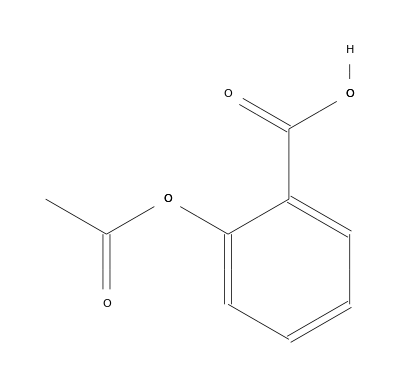

```mathematica
ChemicalData["Aspirin"]
```

Using the "MoleculePlot" option of the ChemicalData command, you can obtain a rotatable ball-and-stick representation of the molecule.  Carbon atoms are represented by a grayish ball;  oxygens by red; hydrogens by white; and nitrogens by blue.  Other atoms are colored using a variety of coloring styles, for example, green for halogens.  Click and hold on the molecule below, and rotate the molecule!

```mathematica
ChemicalData["Aspirin", "MoleculePlot"]
```

-Graphics3D-

```mathematica
ChemicalData["Aspirin", "SpaceFillingMoleculePlot"]
```

We can also display the molecule as a space-filling represenation, which shows an approximation to the actual shape of the molecule.  Space-filling representations, sometimes known as CPK models, are particularly useful in medicinal chemistry when there is a discussion of docking (inserting) a drug into a protein receptor.

-Graphics3D-

It is particularly helpful to be able to clearly describe the chemical structure of the drug.  In the graphic below, you can see a 2D representation that clearly identifies bond types (single, double, etc.) and the relationship of each atom to the overall molecule.

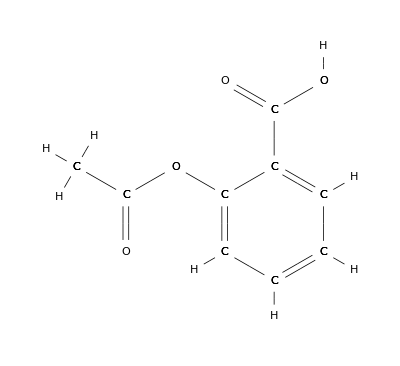

```mathematica
ChemicalData["Aspirin", "CHStructureDiagram"]
```

We can add a little color to the structural diagram, making it easier to see heavy atoms such as oxygen:

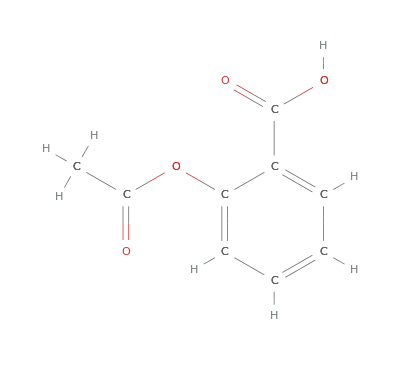

```mathematica
ChemicalData["Aspirin", "CHColorStructureDiagram"]
```

One of the notational systems that will be particularly helpful in the study of medicinal chemistry is the SMILES format.  SMILES format gives us a way of describing the structure of a compound (and which atoms are connected to which) in a text-based string.  You could send a text message over your phone with the structural formula for a compound, and then the recipient could enter that into a computer to see the three-dimensional structure of the molecule!  You should note that SMILES notation is case sensitive -- a capital "C" is different from a lower case "c".

```mathematica
ChemicalData["Aspirin", "SMILES"]
```

CC(=O)OC1=CC=CC=C1C(=O)O

It is important to know the number of atoms in any compound.  Aspirin is pretty easy, you can count the number of carbons, hydrogens, and oxygens by sight.  It is more difficult, however, with larger compounds:

```mathematica
ChemicalData["Aspirin","ElementTally"]
```

{{C,9},{H,8},{O,4}}

This translates into this chemical formula:

```mathematica
ChemicalData["Aspirin", "MolecularFormulaDisplay"]
```

(CH_3CO_2)C_6H_4CO_2H

You can also determine the empirical formula of the compound:

```mathematica
ChemicalData["Aspirin", "CompoundFormulaDisplay"]
```

C_9H_8O_4

You might recall from introductory chemistry the idea of percent composition.  Aspirin is roughly 60% carbon, 5% hydrogen, and 35% oxygen:

```mathematica
ChemicalData["Aspirin", "ElementMassFraction"]
```

{{C,60.001},{H,4.4758},{O,35.523}}

We might also want to count bonds and bond types.  Using BondTally, we see that aspirin has three double bonds between the carbons ({{{"C", "C"}, 2}, 3}), five single carbon-carbon bonds, seven carbon-hydrogen single bonds, two carbon-oxygen double bonds, three carbon-oxygen single bonds, and 1 hydrogen-oxygen single bond.  Make sure you can read this notational system!

```mathematica
ChemicalData["Aspirin", "BondTally"]
```

{{{{C,C},2},3},{{{C,C},1},5},{{{C,H},1},7},{{{C,O},2},2},{{{C,O},1},3},{{{H,O},1},1}}

#### Nomenclature

Medicinal chemists need to be able to talk about compounds in a variety of ways.  The name "aspirin" works well most of the time, but chemists tend to use names that are more informative.  For example, the International Union of Pure and Applied Chemistry (IUPAC) provides a system for naming structures.  The IUPAC name for aspirin, shown below, is a more informative description of the compound.  Once you are familiar with organic naming and functional groups, and you hear the IUPAC name, you will be able to "see" the molecule in your head!

```mathematica
ChemicalData["Aspirin", "IUPACName"]
```

2-acetyloxybenzoic acid

There are typically a number of alternate names for chemical compounds. The most common one of the group shown below is acetylsalicylic acid, also known as "ASA".  Salicylic acid is a non-IUPAC name that comes from the root word for a willow tree, the plant from which aspirin first was discovered.

```mathematica
ChemicalData["Aspirin", "AlternateNames"]
```

{2-acetoxybenzoic acid,2-(acetyloxy)benzoic acid,acenterine,acetosal,acetylsalicylic acid,benzoic acid, 2-(acetyloxy)-}

### General Characteristics

There are some basic characteristics of compounds that medicinal chemists need to know.  Some examples are below:

##### Molecular Weight (grams per mole, or g/mol)

It is likely that you have encountered molecular weight, sometimes known as molar mass, in your introductory chemistry class.  For oral drugs, drugs that have a molecular weight greater than 500 g/mol are typically poor oral drugs (drugs taken by mouth), according to Lipinski rules.

```mathematica
ChemicalData["Aspirin", "MolecularWeight"]
```

180.157

##### Melting point (degrees Celsius)

```mathematica
ChemicalData["Aspirin", "MeltingPoint"]
```

140.

##### Boiling point (degrees Celsius)

```mathematica
ChemicalData["Aspirin", "BoilingPoint"]
```

140.

##### Density (grams per cc g/cc or grams per milliliter g/mL)

```mathematica
ChemicalData["Aspirin","DensityGramsPerCC"]
```

1.39

##### Compound Category, chemical type (organic or inorganic), phase at room temperature

```mathematica
ChemicalData["Aspirin", "Memberships"]
```

{Drugs,Organic,Solids}

### Drug Properties

There are also a wide variety of drug-related properties that we need to know.  If they are not known, they need to be calculated, either experimentally or computationally.  Some examples are shown below:

##### Partition Coefficient (no units)

The partition coefficient, typically listed as the logP value, is a measure of the lipophilicity/hydrophobicity of a drug.  These are parameters that will help the medicinal chemist to predict if the drug can pass through a cell or other tissue membrane.  If the drug can't get through a membrane, it is unlikely to be able to function as a drug.  LogP values for oral drugs (drugs taken by mouth) are typically less than 5, according to Lipinski.  Aspirin has a logP value around 1.4, an indicator that aspirin is a good drug to give orally!

```mathematica
ChemicalData["Aspirin", "PartitionCoefficient"]
```

1.4

##### Topological Polar Surface Area (in units of square angstroms, Å^2)

Topological polar surface area, or TPSA, is a measure of how much of the surface of the molecule has polar characteristics.  Polar surfaces interact differently with other molecules than do nonpolar surfaces, and having some idea of how much polar surface area there is will help to evaluate the effectiveness of a drug.   TPSA is particularly useful in determining if the drug can penetrate a cell membrane.  Drugs with a TPSA higher than 140 Å^2 typically will not penetrate cell membranes.  Drugs that we want to penetrate the blood-brain barrier (BBB) to be able to act on the central nervous system (CNS) need to have a TPSA value in the area of 60 Å^2.

```mathematica
ChemicalData["Aspirin", "TopologicalPolarSurfaceArea"]
```

63.6

##### Number of rotatable bonds

One of the important characteristics of drugs is the number of rotatable bonds that they have.  Drugs can change shape when parts of the compound can rotate around bonds.  Different configurations -- different rotations of rotable bonds -- are known as conformers.  The number rotatable bonds will have a direct impact on how the conformation of the drug.  As shown below, aspirin has three rotatable bonds.  You should look to identify which bonds are rotatable.

```mathematica
ChemicalData["Aspirin"]
ChemicalData["Aspirin", "RotatableBondCount"]
```

-Graphics-

3

In drug chemistry, interactions between the drug and other molecules in the body (typically protein receptors) happens through bonding.  One of the most important types of bonding is hydrogen bonding.  Some molecules can donate hydrogens to the hydrogen bonding process, and some can accept hydrogen bonds.  Most drugs can do both.  We can explore the number of hydrogen bond acceptors and hydrogen bond donors that a drug has.  As below, aspirin has four hydrogen bond acceptors and one hydrogen bond donor:

```mathematica
ChemicalData["Aspirin", "HBondAcceptorCount"]
```

4

```mathematica
ChemicalData["Aspirin", "HBondDonorCount"]
```

1

There are a wide variety of other properties that can be obtained for this chemical (and most others) from the Wolfram databases.  For many compounds, some of these options may result in a "missing not available" error message!

```mathematica
ChemicalData["Aspirin", "Properties"]
```

{AcidityConstant,AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BoilingPoint,BondTally,CASNumber,CHColorStructureDiagram,CHStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CompoundFormulaDisplay,CompoundFormulaString,CriticalPressure,CriticalTemperature,Density,DensityGramsPerCC,DielectricConstant,DOTHazardClass,DOTNumbers,EdgeRules,EdgeTypes,EGECNumber,ElementMassFraction,ElementTally,ElementTypes,EUNumber,FlashPoint,FlashPointFahrenheit,FormalCharges,FormattedName,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HildebrandSolubilitySI,InChI,IonEquivalents,Ions,IonTally,IsoelectricPoint,IsomericSMILES,IUPACName,LogAcidityConstant,LowerExplosiveLimit,MDLNumber,MeltingBehavior,MeltingPoint,Memberships,MolarVolume,MolecularFormulaDisplay,MolecularFormulaString,MolecularWeight,MoleculePlot,Name,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeNumbers,NonStandardIsotopeTally,NSCNumber,OdorThreshold,OdorType,PartitionCoefficient,pH,Phase,RefractiveIndex,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainAcidityConstant,SMILES,Solubility,SolubilityType,SpaceFillingMoleculePlot,StandardName,StructureDiagram,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VaporPressureTorr,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
ChemicalData["Aspirin", "SideChainAcidityConstant"]
```

Missing[NotAvailable]

We can develop a nice table with the drug profile for aspirin.  Not every item from the profile above is included in this table:

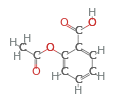
Formula | C_9H_8O_4
IUPAC Name | 2-acetyloxybenzoic acid
Structural Formula | -Graphics-
Percent composition | {{C,60.0},{H,4.47},{O,35.53}}
Molecular Weight (g/mol) | 180.157
Density (g/mL) | 1.39
Number of rotatable bonds | 3
logP | 1.4
TPSA (Å^2) | 63.6
Hydrogen donors | 4
Hydrogen acceptors | 1
SMILES formula | CC(=O)OC1=CC=CC=C1C(=O)O
Classification of compound | Drugs, organic solid

Table 1:  Drug profile for aspirin (acetylsalicylic acid, or ASA)

## Exercise: Drug Profile Practice

You are a medicinal chemist who has been asked to prepare a technical report on valium,  a well-known and frequently used anti-anxiety compound.  Using the appropriate tools, prepare a profile of this drug. You are encouraged to add rows to include more data than is shown in this table.  Include as many parameters as you can find for this compound.  Once you have completed your table, print out the table for your records.

This activity is designed to be completed using Mathematica, but it can also be accomplished using a variety of online resources.  Some of these include:

DrugBank:  http://www.drugbank.ca/

PharmGKB:  http://www.pharmgkb.org/index.jsp

Protein Data Bank: http://www.rcsb.org/pdb/home/home.do

Formula | □
IUPAC Name | □
Structural Formula | 
Percent composition | □
Molecular Weight (g/mol) | □
Density (g/mL) | □
Number of rotatable bonds | □
logP | □
TPSA | □
Hydrogen donors | □
Hydrogen acceptors | □
SMILES formula | □
Classification of compound | □